# Fourier Expansion in a Flare

In this notebook, we compute the Fourier expansion for a Maass form in a flare domain.

## The Differential Equation

Here is the expression such that expr = 0 is our ODE of interest. The ODE is second order; we require the solution to be L^2 on an infinite volume fundamental domain (should be the solution which goes to 0 faster as x goes to 0).

```mathematica
expr = Sin[x]^2(g''[x] + (2Pi I n/k)^2g[x]) + s(1 - s)g[x]
```

(1-s) s g[x]+Sin[x]^2 (-(4 n^2 π^2 g[x])/k^2+g''[x])

```mathematica
expr // Simplify
```

-((-1+s) s g[x])+Sin[x]^2 (-(4 n^2 π^2 g[x])/k^2+g''[x])

## Solving the Equation

Here we check if Mathematica can find a solution right away.

```mathematica
soln = DSolve[expr == 0, g[x], x]
```

{{g[x]→C[1] (-1+Cos[x]^2)^(1/4) LegendreP[(ⅈ (ⅈ k+4 n π))/(2 k),1/2 (-1+2 s),Cos[x]]+C[2] (-1+Cos[x]^2)^(1/4) LegendreQ[(ⅈ (ⅈ k+4 n π))/(2 k),1/2 (-1+2 s),Cos[x]]}}

```mathematica
?LegendreP
```

Not bad! What if we help out with some assumptions?

```mathematica
solnReal = Assuming[{s ∈ Reals, 0 < s, s < 1, k ∈ Reals, k > 0}, DSolve[expr == 0, g[x], x]]
```

{{g[x]→C[1] (-1+Cos[x]^2)^(1/4) LegendreP[(ⅈ (ⅈ k+4 n π))/(2 k),1/2 (-1+2 s),Cos[x]]+C[2] (-1+Cos[x]^2)^(1/4) LegendreQ[(ⅈ (ⅈ k+4 n π))/(2 k),1/2 (-1+2 s),Cos[x]]}}

Didn’t change anything. Let’s form the two solutions and check which is smaller as x -> 0.
Note: we replace the term in front of the Legendre functions with sqrt(x), since we can multiply a solution to a homogeneous equation by a constant to get rid of the I.

```mathematica
g1 = (Sin[x])^(1/2) LegendreP[(ⅈ (ⅈ k+4 n π))/(2 k),1/2 (-1+2 s),Cos[x]]
```

LegendreP[(ⅈ (ⅈ k+4 n π))/(2 k),1/2 (-1+2 s),Cos[x]] √Sin[x]

```mathematica
g2 = (Sin[x])^(1/2) LegendreQ[(ⅈ (ⅈ k+4 n π))/(2 k),1/2 (-1+2 s),Cos[x]]
```

LegendreQ[(ⅈ (ⅈ k+4 n π))/(2 k),1/2 (-1+2 s),Cos[x]] √Sin[x]

```mathematica
G1[{X_, N_, K_, S_}] = g1 /. x -> X /. n -> N /. k ->K /. s -> S
```

LegendreP[(ⅈ (ⅈ K+4 N π))/(2 K),1/2 (-1+2 S),Cos[X]] √Sin[X]

```mathematica
G2[{X_, N_, K_, S_}] = g2 /. x -> X /. n -> N /. k ->K /. s -> S
```

LegendreQ[(ⅈ (ⅈ K+4 N π))/(2 K),1/2 (-1+2 S),Cos[X]] √Sin[X]

```mathematica
points = {{Pi/4, 1, 2, 0.6}, {Pi/4, 2, 2, 0.8}, {Pi/16, 1, 2, 0.6}, {Pi/16, 2, 2, 0.8}, {Pi/64, 1, 2, 0.6}, {Pi/64, 2, 2, 0.8}, {Pi/256, 1, 2, 0.6}, {Pi/256, 2, 2, 0.8}}
```

{{π/4,1,2,0.6},{π/4,2,2,0.8},{π/16,1,2,0.6},{π/16,2,2,0.8},{π/64,1,2,0.6},{π/64,2,2,0.8},{π/256,1,2,0.6},{π/256,2,2,0.8}}

```mathematica
Map[G1, points]
```

{3.16009+6.16658×10^-17 ⅈ,38.9952+3.66328×10^-17 ⅈ,0.579188-1.59629×10^-21 ⅈ,1.10023-1.6951×10^-18 ⅈ,0.302346+2.67775×10^-22 ⅈ,0.536784-7.62225×10^-20 ⅈ,0.172591-6.00859×10^-25 ⅈ,0.394201-4.32653×10^-39 ⅈ}

```mathematica
Map[G2, points]
```

{0.0621195-4.94368 ⅈ,0.00362773-61.2485 ⅈ,0.360497-0.792654 ⅈ,0.141545-1.53342 ⅈ,0.480194-0.3189 ⅈ,0.328512-0.391021 ⅈ,0.409303-0.138114 ⅈ,0.357751-0.126808 ⅈ}

Not a huge difference... what about as n gets large?

```mathematica
points2 = {{Pi/4, 10, 2, 0.6}, {Pi/4, 20, 2, 0.8}, {Pi/16, 10, 2, 0.6}, {Pi/16, 20, 2, 0.8}, {Pi/64, 10, 2, 0.6}, {Pi/64, 20, 2, 0.8}, {Pi/256, 100, 2, 0.6}, {Pi/256, 200, 2, 0.8}}
```

{{π/4,10,2,0.6},{π/4,20,2,0.8},{π/16,10,2,0.6},{π/16,20,2,0.8},{π/64,10,2,0.6},{π/64,20,2,0.8},{π/256,100,2,0.6},{π/256,200,2,0.8}}

```mathematica
Map[G1, points2]
```

{5.24263×10^9+0. ⅈ,4.71421×10^20+0. ⅈ,48.9997+8.06372×10^-18 ⅈ,40001.2+0. ⅈ,0.532031-2.75287×10^-19 ⅈ,3.94244-7.26619×10^-19 ⅈ,1.96165+1.38699×10^-18 ⅈ,248.202+0. ⅈ}

```mathematica
Map[G2, points2]
```

{0.00062777-8.2351×10^9 ⅈ,-5.11461×10^7-7.40506×10^20 ⅈ,0.000617616-76.9683 ⅈ,1.40204×10^-6-62833.8 ⅈ,0.0603826-0.816092 ⅈ,0.0143986-6.17295 ⅈ,0.00246012-3.08055 ⅈ,0.0000900976-389.875 ⅈ}

I think g1 is the right choice, but this bears more thought...

## Solution when s is on 1/2 Line

Recall that s is either real with 0 < s < 1 or s = 1/2 + i t for some real t. Let’s force the assumption on t and see if this changes the solution.

```mathematica
exprt = expr /. s -> 1/2 + I*t // Simplify
```

g[x] (1/4+t^2-(4 n^2 π^2 Sin[x]^2)/k^2)+Sin[x]^2 g''[x]

```mathematica
solnt = Assuming[{t ∈ Reals, 0 < t, k ∈ Reals, k > 0}, DSolve[exprt == 0, g[x], x]]
```

{{g[x]→C[1] (-1+Cos[x]^2)^(1/4) LegendreP[(ⅈ (ⅈ k+4 n π))/(2 k),ⅈ t,Cos[x]]+C[2] (-1+Cos[x]^2)^(1/4) LegendreQ[(ⅈ (ⅈ k+4 n π))/(2 k),ⅈ t,Cos[x]]}}

This is the same answer as before BUT maybe the different arguments will cause us to switch solutions? Let’s plug some values in...

```mathematica
h1 = Sqrt[Sin[x]]LegendreP[(ⅈ (ⅈ k+4 n π))/(2 k),ⅈ t,Cos[x]]
```

LegendreP[(ⅈ (ⅈ k+4 n π))/(2 k),ⅈ t,Cos[x]] √Sin[x]

```mathematica
h2 = Sqrt[Sin[x]]LegendreQ[(ⅈ (ⅈ k+4 n π))/(2 k),ⅈ t,Cos[x]]
```

LegendreQ[(ⅈ (ⅈ k+4 n π))/(2 k),ⅈ t,Cos[x]] √Sin[x]

```mathematica
H1[{X_, N_, K_, T_}] = h1 /. x -> X /. n -> N /. k ->K /. t -> T
```

LegendreP[(ⅈ (ⅈ K+4 N π))/(2 K),ⅈ T,Cos[X]] √Sin[X]

```mathematica
H2[{X_, N_, K_, T_}] = h2 /. x -> X /. n -> N /. k ->K /. t -> T
```

LegendreQ[(ⅈ (ⅈ K+4 N π))/(2 K),ⅈ T,Cos[X]] √Sin[X]

```mathematica
pointst= {{Pi/4, 1, 2, 4.3}, {Pi/4, 2, 2, 4.3}, {Pi/256, 1, 2, 4.3}, {Pi/256, 2, 2, 4.3}, {Pi/4, 10, 2, 4.3}, {Pi/4, 20, 2, 4.3}, {Pi/256, 10, 2, 4.3}, {Pi/256, 20, 2, 4.3}}
```

{{π/4,1,2,4.3},{π/4,2,2,4.3},{π/256,1,2,4.3},{π/256,2,2,4.3},{π/4,10,2,4.3},{π/4,20,2,4.3},{π/256,10,2,4.3},{π/256,20,2,4.3}}

```mathematica
Map[H1, pointst]
```

{124.781+82.8821 ⅈ,-19.0502+218.581 ⅈ,16.1123-8.64026 ⅈ,16.1154-8.63679 ⅈ,-3.14297×10^9+3.94599×10^9 ⅈ,7.8876×10^19-1.3718×10^20 ⅈ,16.2126-8.52525 ⅈ,16.5136-8.17014 ⅈ}

```mathematica
Map[H2, pointst]
```

{130.191-196.006 ⅈ,343.347+29.924 ⅈ,-13.5721-25.3092 ⅈ,-13.5666-25.314 ⅈ,6.19835×10^9+4.93696×10^9 ⅈ,-2.15482×10^20-1.23898×10^20 ⅈ,-13.3914-25.4667 ⅈ,-12.8336-25.9395 ⅈ}

```mathematica
{Arg[124.78136314548343+82.88206224135112 ⅈ], Arg[-19.050225737257687+218.58134885396015 ⅈ], Arg[16.112329490656155-8.64025754491169 ⅈ]}
```

{0.586306,1.65773,-0.492226}

## When n = 0

```mathematica
expr0 = Sin[x]^2g''[x] + s(1 - s)g[x]
```

(1-s) s g[x]+Sin[x]^2 g''[x]

```mathematica
soln = DSolve[expr0 == 0, g[x], x]
```

{{g[x]→C[1] (-1+Cos[x]^2)^(1/4) LegendreP[-1/2,1/2 (-1+2 s),Cos[x]]+C[2] (-1+Cos[x]^2)^(1/4) LegendreQ[-1/2,1/2 (-1+2 s),Cos[x]]}}

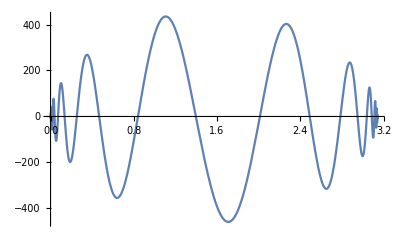

```mathematica
Plot[Re[Sqrt[Sin[x]]LegendreP[-1/2,1/2 (-1+2 s)/.s -> 1/2 + 5I,Cos[x]]], {x, 0, Pi}]
```

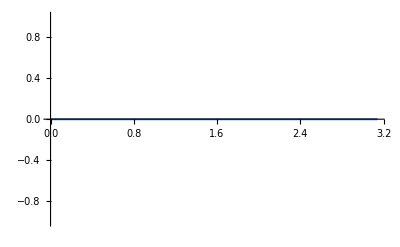

```mathematica
Plot[Im[Sqrt[Sin[x]]LegendreP[-1/2,1/2 (-1+2 s)/.s -> 1/2 + 0.1,Cos[x]]], {x, 0, Pi}]
```